## advection1_LF_test

{f→Function[{x,t},1. ⅇ^(-t-10. (-1.+ⅇ^-t x)^2-10. (1.+ⅇ^-t x)^2) (1. ⅇ^(10. (-1.+ⅇ^-t x)^2)+1. ⅇ^(10. (1.+ⅇ^-t x)^2))]}

1. ⅇ^(-t-10. (-1.+ⅇ^-t x)^2-10. (1.+ⅇ^-t x)^2) (1. ⅇ^(10. (-1.+ⅇ^-t x)^2)+1. ⅇ^(10. (1.+ⅇ^-t x)^2))

{True}

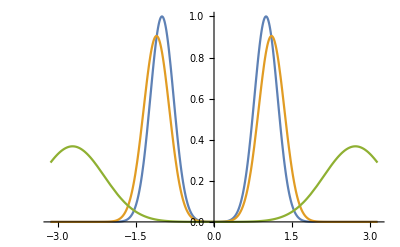

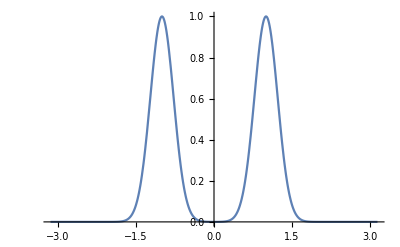

```mathematica
ClearAll["Global`*"];
eq=D[f[x,t],t]==-D[x f[x,t],x];
sig=0.1;
f0=Exp[-(x-1)^2/sig]+Exp[-(x+1)^2/sig];
sol = DSolve[{eq,f[x,0]==f0},f,{x,t}];
sol[[1]]
ff[x_,t_]=f[x,t]/.sol[[1]]
FullSimplify[eq/.sol]
Plot[{ff[x,0],ff[x,0.1],ff[x,1]},{x,-Pi, Pi}]
```